```mathematica
Needs["NDSolve`FEM`"]
SetSystemOptions["FiniteElementOptions"->{"DefaultNumberOfElements"->10}];
SetSystemOptions["FiniteElementOptions"->{"InterpolationToleranceFactor"->1.}];
SetSystemOptions["FiniteElementOptions"->{"SymbolicProcessing"->100.}]
```

FiniteElementOptions→{CacheInterpolationElements→True,DefaultBounds→{-1,1},DefaultElementMeshOrder→2,DefaultExtrapolationHandler→{Indeterminate&,WarningMessage→True},DefaultNumberOfElements→10,InterpolationToleranceFactor→1.,MinimumElementMeshQuality→0.,SymbolicProcessing→100.}

```mathematica
hull1=ImplicitRegion[(z≤10.&&z≥2.215384615384615+1.159647461884313 x^2.&&0.<y≤ 10.),{x,y,z}];
hull2=ImplicitRegion[(z≤10.&&z≥0.7538461538461538+0.3102990715481003 x^2.&&10.≤ y≤ 20.),{x,y,z}];
hull3=ImplicitRegion[(z≤10.&&z≥0.061538461538461535+0.16809777948184113 x^2.&&20.≤ y≤ 30.),{x,y,z}];
hull4=ImplicitRegion[(z≤10.&&z≥0.13846153846153844+0.11225568226713982 x^2.&&30.≤ y≤ 40.),{x,y,z}];
hull5=ImplicitRegion[(z≤10.&&z≥0.9846153846153846+0.08302998710242387 x^2.&&40.≤ y≤ 50.),{x,y,z}];
hull6=ImplicitRegion[(z≤10.&&z≥2.6+0.06526115558326687 x^2.&&50.≤ y<58.),{x,y,z}];
hullreg =RegionUnion[hull1,hull2,hull3, hull4, hull5, hull6]

waterdensity = 1.
Volume[hullreg]
```

ImplicitRegion[z≤10.&&((z≥2.21538+1.15965 x^2.&&y>0&&y≤10.)||(z≥2.6+0.0652612 x^2.&&y<58.&&y≥50.)||(z≥0.984615+0.08303 x^2.&&y≥40.&&y≤50.)||(z≥0.138462+0.112256 x^2.&&y≥30.&&y≤40.)||(z≥0.0615385+0.168098 x^2.&&y≥20.&&y≤30.)||(z≥0.753846+0.310299 x^2.&&y≥10.&&y≤20.)),{x,y,z}]

1.

5286.28

```mathematica
Mass[boatregion_, boatdensity_]:=1400.
boatmass=1000.
boatcom = {0,34.16, 2.5}
```

1000.

{0,34.16,2.5}

```mathematica
1400.
```

1400.

```mathematica
Waterline3D[θ_, ϕ_]:= Quiet[ImplicitRegion[Piecewise[{{y, ϕ==90},{x, θ==90},{-z, θ>90||ϕ>90}},z]≤Piecewise[{{draft, θ==90||ϕ==90},{-1*(Tan[θ*π/180]*x+Tan[ϕ*π/180]*y+draft), θ>90||ϕ>90}},Tan[θ*π/180]*x+Tan[ϕ*π/180]*y+draft],{{x,-15,15}, {y,0,60}, {z,0,30}}]]
CalculateDraft3D[boatregion_, θ_, ϕ_]:=Quiet[FindRoot[Integrate[1., {x,y,z}∈RegionIntersection[boatregion, Waterline3D[θ, ϕ]]]==boatmass/1.,{draft, 1-Tan[θ*π/180]/3-Tan[ϕ*π/180]/3}][[1]]]
DisplacedWater3D[boatregion_, θ_, ϕ_]:= Quiet[RegionIntersection[boatregion, Waterline3D[θ, ϕ]]/.CalculateDraft3D[boatregion, θ, ϕ]]
CenterOfBuoyancy3D[boatregion_,θ_, ϕ_]:=Quiet[RegionCentroid[DisplacedWater3D[boatregion,  θ, ϕ]]]
RightingMoment3D[boatregion_, θ_, ϕ_]:=Quiet[Cross[CenterOfBuoyancy3D[boatregion, θ, ϕ]-boatcom, boatmass*9.8*0.001*{-Tan[θ*π/180], -Tan[ϕ*π/180],1}/Piecewise[{{-1, θ>90||ϕ>90}},1]/Norm[{-Tan[θ*π/180], -Tan[ϕ*π/180],1}]]]
```

```mathematica
f[angle1_, angle2_]:=N[RightingMoment3D[hullreg, angle1, angle2]]
angleTable1=Quiet[Parallelize[Table[{angle1, 0.,f[angle1,0.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable2=Quiet[Parallelize[Table[{angle1, 2.,f[angle1,2.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable3=Quiet[Parallelize[Table[{angle1, 4.,f[angle1,4.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable4=Quiet[Parallelize[Table[{angle1, 6.,f[angle1,6.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable5=Quiet[Parallelize[Table[{angle1, 8.,f[angle1,8.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable6=Quiet[Parallelize[Table[{angle1, 10.,f[angle1,10.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable7=Quiet[Parallelize[Table[{angle1, 12.,f[angle1,12.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable8=Quiet[Parallelize[Table[{angle1, 14.,f[angle1,14.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
(*angleTable9=Quiet[Parallelize[Table[{angle1, 16.,f[angle1,16.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable10=Quiet[Parallelize[Table[{angle1, 18.,f[angle1,18.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
angleTable11=Quiet[Parallelize[Table[{angle1, 20.,f[angle1,20.]},{angle1,1.,176.,5.}]]];//AbsoluteTiming
*)
data = Union[angleTable1, angleTable2, angleTable3, angleTable4, angleTable5, angleTable6,angleTable7, angleTable8];
xdata = Table[{data[[i, 1]], data[[i, 2]], data[[i, 3, 1]]}, {i, 1, Length[data],1}];
ydata = Table[{data[[i, 1]], data[[i, 2]], data[[i, 3, 2]]}, {i, 1, Length[data],1}];
zdata = Table[{data[[i, 1]], data[[i, 2]], data[[i, 3, 3]]}, {i, 1, Length[data],1}];
normdata = Quiet[Parallelize[Table[{data[[i, 1]], data[[i, 2]], Quiet[Norm[data[[i, 3]]]]}, {i, 1, Length[data],1}]]];
Quiet[ListPlot3D[normdata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]]
Show[ListPlot3D[ydata,PlotRange->{{120,140},{0,15},{-1,1}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],ListPlot3D[xdata,PlotRange->{{120,140},{0,15},{-1,1}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]]
ListPlot3D[xdata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
ListPlot3D[ydata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

{26.0177,Null}

{79.8654,Null}

{80.8967,Null}

{77.2835,Null}

{84.8212,Null}

{87.1419,Null}

{84.2689,Null}

{86.2903,Null}

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Show[ListPlot3D[ydata,PlotRange->{{120,140},{0,15},{-10,0}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],ListPlot3D[xdata,PlotRange->{{120,140},{0,15},{-10,0}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],ListPlot3D[zdata,PlotRange->{{120,140},{0,15},{-10,0}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]]
ListPlot3D[xdata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
ListPlot3D[ydata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
ListPlot3D[zdata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
RightingMoment3D[hullreg,0.,0.]
RightingMoment3D[hullreg,0.,1.]
boatcom
```

{-15.8779,-2.69829×10^-16,0.}

{0.727655,6.35306×10^-16,1.10893×10^-17}

{0,34.16,3.5}

```mathematica
data = Union[angleTable1, angleTable2, angleTable3, angleTable4, angleTable5, angleTable6, angleTable7,angleTable9, angleTable10, angleTable11];
```

```mathematica
xdata = Table[{data[[i, 1]], data[[i, 2]], data[[i, 3, 1]]}, {i, 1, Length[data],1}];
ydata = Table[{data[[i, 1]], data[[i, 2]], data[[i, 3, 2]]}, {i, 1, Length[data],1}];
```

```mathematica
ListPlot3D[xdata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
ListPlot3D[xdata,PlotRange->{-10,10},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

-Graphics3D-

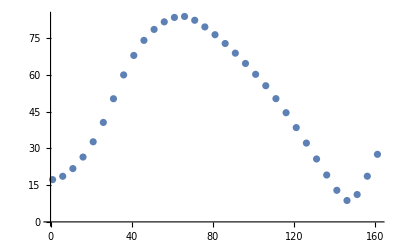

FindRoot::nlnum: The function value {2.46367×10^-6 (-2.54046×10^7+70512.8 √(Times[«2»]+Power[«2»]+Power[«2»])+854970. √(Times[«2»]+Power[«2»]+Power[«2»])-379557. √(Times[«2»]+Power[«2»]+Power[«2»]))+7.84904×10^-8 (-1.03041×10^7+40347.6 √(Times[«2»]+Power[«2»]+Power[«2»])+338707. √(Times[«2»]+Power[«2»]+Power[«2»])-155331. √(Times[«2»]+Power[«2»]+Power[«2»]))+«7»+0.0000136346 (1.78536×10^7-39710.1 √(Times[«2»]+Power[«2»]+Power[«2»])-619272. √(Times[«2»]+Power[«2»]+Power[«2»])+270792. √(Times[«2»]+Power[«2»]+Power[«2»]))+4.4125×10^-7 (2.17758×10^7-72668.8 √(Times[«2»]+Power[«2»]+Power[«2»])-720683. √(Times[«2»]+Power[«2»]+Power[«2»])+325056. √(Times[«2»]+Power[«2»]+Power[«2»]))} is not a list of numbers with dimensions {1} at {x} = {30.}.

FindMinimum::nrnum: The function value 0.+0.166667 (117.458+0.0232254 √(1. Power[«2»]+Abs[«1»]^2+Abs[«1»]^2)-0.568716 √(1. Power[«2»]+Abs[«1»]^2+Abs[«1»]^2)+0.230492 √(1. Power[«2»]+Abs[«1»]^2+Abs[«1»]^2)) is not a real number at {x} = {0.}.

FindMinimum[bestFit,{x,0}]

FindRoot::nlnum: The function value {2.46367×10^-6 (-2.54046×10^7+70512.8 √(Times[«2»]+Power[«2»]+Power[«2»])+854970. √(Times[«2»]+Power[«2»]+Power[«2»])-379557. √(Times[«2»]+Power[«2»]+Power[«2»]))+7.84904×10^-8 (-1.03041×10^7+40347.6 √(Times[«2»]+Power[«2»]+Power[«2»])+338707. √(Times[«2»]+Power[«2»]+Power[«2»])-155331. √(Times[«2»]+Power[«2»]+Power[«2»]))+«7»+0.0000136346 (1.78536×10^7-39710.1 √(Times[«2»]+Power[«2»]+Power[«2»])-619272. √(Times[«2»]+Power[«2»]+Power[«2»])+270792. √(Times[«2»]+Power[«2»]+Power[«2»]))+4.4125×10^-7 (2.17758×10^7-72668.8 √(Times[«2»]+Power[«2»]+Power[«2»])-720683. √(Times[«2»]+Power[«2»]+Power[«2»])+325056. √(Times[«2»]+Power[«2»]+Power[«2»]))} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {2.46367×10^-6 (-2.54046×10^7+70512.8 √(Times[«2»]+Power[«2»]+Power[«2»])+854970. √(Times[«2»]+Power[«2»]+Power[«2»])-379557. √(Times[«2»]+Power[«2»]+Power[«2»]))+7.84904×10^-8 (-1.03041×10^7+40347.6 √(Times[«2»]+Power[«2»]+Power[«2»])+338707. √(Times[«2»]+Power[«2»]+Power[«2»])-155331. √(Times[«2»]+Power[«2»]+Power[«2»]))+«7»+0.0000136346 (1.78536×10^7-39710.1 √(Times[«2»]+Power[«2»]+Power[«2»])-619272. √(Times[«2»]+Power[«2»]+Power[«2»])+270792. √(Times[«2»]+Power[«2»]+Power[«2»]))+4.4125×10^-7 (2.17758×10^7-72668.8 √(Times[«2»]+Power[«2»]+Power[«2»])-720683. √(Times[«2»]+Power[«2»]+Power[«2»])+325056. √(Times[«2»]+Power[«2»]+Power[«2»]))} is not a list of numbers with dimensions {1} at {x} = {30.}.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {2.46367×10^-6 (-2.54046×10^7+70512.8 √(Times[«2»]+Power[«2»]+Power[«2»])+854970. √(Times[«2»]+Power[«2»]+Power[«2»])-379557. √(Times[«2»]+Power[«2»]+Power[«2»]))+7.84904×10^-8 (-1.03041×10^7+40347.6 √(Times[«2»]+Power[«2»]+Power[«2»])+338707. √(Times[«2»]+Power[«2»]+Power[«2»])-155331. √(Times[«2»]+Power[«2»]+Power[«2»]))+«7»+0.0000136346 (1.78536×10^7-39710.1 √(Times[«2»]+Power[«2»]+Power[«2»])-619272. √(Times[«2»]+Power[«2»]+Power[«2»])+270792. √(Times[«2»]+Power[«2»]+Power[«2»]))+4.4125×10^-7 (2.17758×10^7-72668.8 √(Times[«2»]+Power[«2»]+Power[«2»])-720683. √(Times[«2»]+Power[«2»]+Power[«2»])+325056. √(Times[«2»]+Power[«2»]+Power[«2»]))} is not a list of numbers with dimensions {1} at {x} = {30.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Part::partd: Part specification FindRoot[bestFit,{x,30}]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

5 FindRoot[bestFit,{x,30}]⟦1,2⟧

```mathematica
heeldata = Table[{angleTable2[[i, 1]], Norm[angleTable2[[i, 3]]]}, {i, 1, Length[angleTable2],1}];
bestFit=Fit[heeldata,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Plot[bestFit,{x,0,180}];
ListPlot[heeldata];
Show[%,%%]
root=FindRoot[bestFit,{x,30}];
maxTorque=FindMinimum[bestFit,{x,0}]
avs=root[[1,2]]*5
```

```mathematica
data2= Union[angleTable1, angleTable2, angleTable3, angleTable4, angleTable5, angleTable6, angleTable7,angleTable9, angleTable10, angleTable11, angleTable12, angleTable13, angleTable14, angleTable15, angleTable16];
```

```mathematica
ListPlot3D[ydata,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
ListPlot3D[ydata,PlotRange->{-10,10},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[ListPlot3D[ydata,PlotRange->{{100,140},{0,15},{-10,10}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],ListPlot3D[xdata,PlotRange->{{100,140},{0,15},{-10,10}},Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]]
```

-Graphics3D-

```mathematica
ZeroCurvePoints[data_]:= Module[{dat = data},
row = Count[angleTable1];
phiOfTheta = {0,0};
For[i = 1, i<row+1, i++,
For[j = 1, j<Count[dat]/row, j++, 
point =dat[[i+row*j]];
up =dat[[i+row*(j-1)]];
If[point[[3]]*down[[3]]≤ 0,Append[phiOfTheta,point[[{1,2}]]] ,Null];
];
];
phiOfTheta
]
```

```mathematica
ZeroCurvePoints[xdata]
```

{0,0}

Point of intersection of the planes is AVS!!!!!! ~140 for this boat